# Задание 06.

## Списки

## Мосейков Игнатий Геннадьевич, группа №21372

Обратите внимание на раздел справки по применению функций к спискам (ссылка: Applying Functions to Lists), особенно на функциональный подход к программированию. Разберитесь как работают наиболее часто используемые функции Map, Apply, Thread, Through, Outer, Inner, которые позволяют распространять действие функций на списки значений разными способами.

Не обязательно, но полезно просмотреть материалы о функциональных операциях в целом в Wolfram Mathematica (ссылка: Functional Operations)

## 1. Итерации vs функциональный подход vs встроенная функция

Напишите три функции, которые принимают список и вычисляют сумму элементов в списке:
1) используя процедурный подход через цикл (Do) и обновлением результата суммирования во временной переменной
2) используя функциональный подход (Apply[Plus, list])
3) используя встроенную функцию (Total)

В Mathematica есть встроенные функции измерения времени выполнения операций (например, Timing). Используя ее, постройте графики времени выполнения от количества элементов в списке (для длины списка порядка 10^6 вычисления уже занимают заметное время; для отрисовки может полезна функция ListLogLogPlot для дважды логарифмического масштаба)

В качестве списка попробуйте передавать предварительно созданный список
- натуральных чисел от 1 до n (Range)
- из n случайных чисел (целых или вещественных RandomReal, RandomInteger)
- список n символьных значений {x, 2x, 3x, ..., n x}, где x — символ

По результатам сделайте выводы об эффективности подходов

```mathematica
fDo[x_]:=Block[{S=0},Do[S+=x[[n]],{n,1,Length[x]}];S];
fApply[x_]:=Apply[Plus,x];
fTotal[x_]:=Total[x];
```

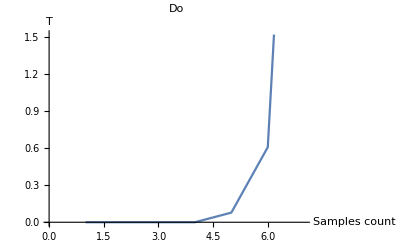

```mathematica
ListLinePlot[Table[Timing[fDo[Range[n]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Do"]
```

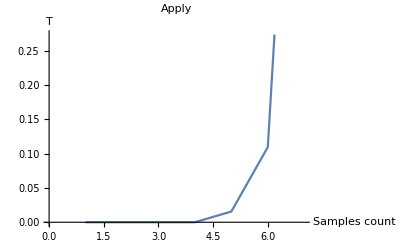

```mathematica
ListLinePlot[Table[Timing[fApply[Range[n]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Apply"]
```

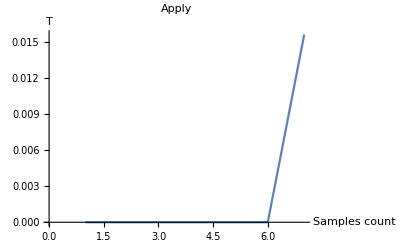

```mathematica
ListLinePlot[Table[Timing[fTotal[Range[n]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Apply"]
```

(RANGE) Total выполняется быстрее.

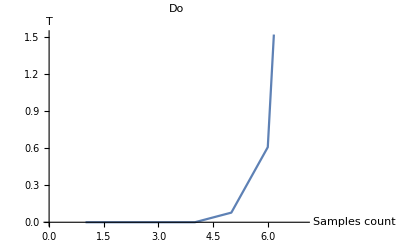

```mathematica
ListLinePlot[Table[Timing[fDo[RandomReal[1,{n}]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Do"]
```

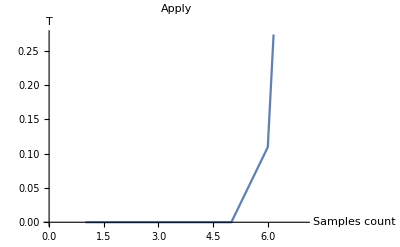

```mathematica
ListLinePlot[Table[Timing[fApply[RandomReal[1,{n}]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Apply"]
```

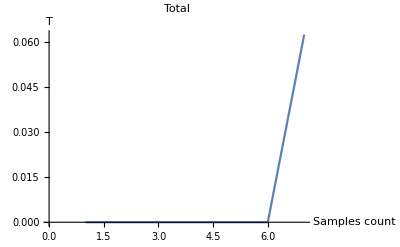

```mathematica
ListLinePlot[Table[Timing[fTotal[RandomReal[1,{n}]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Total"]
```

(RANDOM) Total все еще быстрее. НО! Относительно (RANGE) он медленнее.

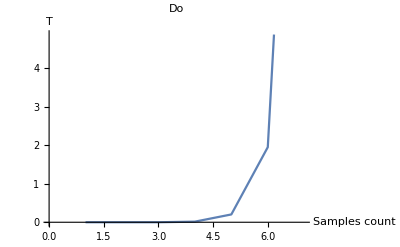

```mathematica
ListLinePlot[Table[Timing[fDo[Table[n*x,{n}]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Do"]
```

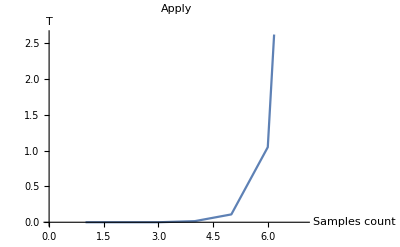

```mathematica
ListLinePlot[Table[Timing[fApply[Table[n*x,{n}]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Samples count", "T"},PlotLabel->"Apply"]
```

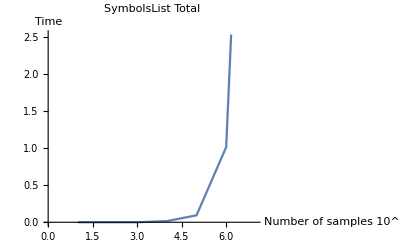

```mathematica
ListLinePlot[Table[Timing[fTotal[Table[n*x,{n}]]][[1]],{n,{10^i}},{i,1,7}],AxesLabel->{"Number of samples 10^i", "Time"},PlotLabel->"SymbolsList Total"]
```

(LIST)  Total все еще самый быстрый, но медленнее относительно (RANDOM)
Total RANGE - fastest!

## 2. Применение функций к спискам

В данном задании не используйте явные циклы или доступ к индексам! Постарайтесь найти подходящую конструкцию в функциональном подходе или встроенную функцию

1) Напишите функцию, на вход которой подаются списки одинаковой длины: сначала идут списки значений (один или несколько), последним всегда идет список меток. Функция должна сформировать список правил (Rule, →) из списка значений в список меток. (эту функцию можно будет использовать в самом последнем пункте задачи про Титаник ниже)

g[{x,y,z},{a,b,c},{0.9,0.1,0.2}, {1,2,3}] = {{x,a,0.9}→1,{y,b,0.1}→2,{z,c,0.2}→3}
g[{x,y,z}, {1,2,3}] = {{x}→1,{y}→2,{z}→3}

```mathematica
g[x_,y_]:=Thread[x->y];
```

```mathematica
g[{x,y,z}, {1,2,3}]
```

{x→1,y→2,z→3}

2) На вход подается два списка (не обязательно одинаковой длины): список функций и список переменных. Напишите функцию, которая бы выдавала матрицу неопределенных первых интегралов по этим переменным. Пример для двух функций и двух переменных

h[{f_1, f_2}, {x, y}}]=(∫f_1 ⅆx  | ∫f_1 ⅆy
∫f_2 ⅆx  | ∫f_2 ⅆy ),

```mathematica
h[x_,y_]:=Outer[Integrate,x, y]//MatrixForm;
```

3) Напишите функцию для вычисления дивергенции (аналог встроенной функции Div) на вход подается два списка одинаковой длины: список функций и список переменных.

div[{f_1, f_2}, {x, y}]=(∂f_1)/(∂x)+(∂f_2)/(∂y)

```mathematica
div[x_,y_]:=Total[Diagonal[D[x,{y}]]];
```

## 3. “Титаник”

1) Данные о пассажирах хранятся в виде csv файла (titanic.csv). Cохраните его в директории с ноутбуком и загрузите данные с помощью функции Import:

```mathematica
SetDirectory[NotebookDirectory[]]; (* чтобы загружать файл из директории, в которой находится ноутбук*)
data = Import["titanic.csv"]
```

{{PassengerId,Survived,Pclass,Name,Sex,Age,SibSp,Parch,Ticket,Fare,Cabin,Embarked},{1,0,3,Braund, Mr. Owen Harris,male,22,1,0,A/5 21171,7.25,,S},{2,1,1,Cumings, Mrs. John Bradley (Florence Briggs Thayer),female,38,1,0,PC 17599,71.2833,C85,C},887,{890,1,1,Behr, Mr. Karl Howell,male,26,0,0,111369,30,C148,C},{891,0,3,Dooley, Mr. Patrick,male,32,0,0,370376,7.75,,Q}}
 |  |  |  |

Обратите внимание, что данные data окажутся в виде списка списков (~таблицы).

2) Выведите заголовки столбцов

```mathematica
data[[1]]
```

{PassengerId,Survived,Pclass,Name,Sex,Age,SibSp,Parch,Ticket,Fare,Cabin,Embarked}

3) Данные о скольких пассажиров у вас имеются?

```mathematica
Length[data]-1
```

891

4) Сохраните данные столбцов "Pclass", "Sex", "Age" и отметки “Survived” в виде отдельных  переменных - списков, с которыми будет удобнее работать в дальнейшем.

```mathematica
pclass = data[[2;;,3]]
sex = data[[2;;,5]]
age = data[[2;;,6]]
survived = data[[2;;,2]]
```

{3,1,3,1,3,3,1,3,3,2,3,1,3,3,3,2,3,2,3,3,2,2,3,1,3,3,3,1,3,3,1,1,3,2,1,1,3,3,3,3,3,2,3,2,3,3,3,3,3,3,3,3,1,2,1,1,2,3,2,3,3,1,1,3,1,3,2,3,3,3,2,3,2,3,3,3,3,3,2,3,3,3,3,1,2,3,3,3,1,3,3,3,1,3,3,3,1,1,2,2,3,3,1,3,3,3,3,3,3,3,1,3,3,3,3,3,3,2,1,3,2,3,2,2,1,3,3,3,3,3,3,3,3,2,2,2,1,1,3,1,3,3,3,3,2,2,3,3,2,2,2,1,3,3,3,1,3,3,3,3,3,2,3,3,3,3,1,3,1,3,1,3,3,3,1,3,3,1,2,3,3,2,3,2,3,1,3,1,3,3,2,2,3,2,1,1,3,3,3,2,3,3,3,3,3,3,3,3,3,1,3,2,3,2,3,1,3,2,1,2,3,2,3,3,1,3,2,3,2,3,1,3,2,3,2,3,2,2,2,2,3,3,2,3,3,1,3,2,1,2,3,3,1,3,3,3,1,1,1,2,3,3,1,1,3,2,3,3,1,1,1,3,2,1,3,1,3,2,3,3,3,3,3,3,1,3,3,3,2,3,1,1,2,3,3,1,3,1,1,1,3,3,3,2,3,1,1,1,2,1,1,1,2,3,2,3,2,2,1,1,3,3,2,2,3,1,3,2,3,1,3,1,1,3,1,3,1,1,3,1,2,1,2,2,2,2,2,3,3,3,3,1,3,3,3,3,1,2,3,3,3,2,3,3,3,3,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,3,1,3,2,3,2,3,2,1,3,3,1,3,3,3,2,2,2,3,3,3,3,3,2,3,2,3,3,3,3,1,2,3,3,2,2,2,3,3,3,3,3,3,3,2,2,3,3,1,3,2,3,1,1,3,2,1,2,2,3,3,2,3,1,2,1,3,1,2,3,1,1,3,3,1,1,2,3,1,3,1,2,3,3,2,1,3,3,3,3,2,2,3,1,2,3,3,3,3,2,3,3,1,3,1,1,3,3,3,3,1,1,3,3,1,3,1,3,3,3,3,3,1,1,2,1,3,3,3,3,1,1,3,1,2,3,2,3,1,3,3,1,3,3,2,1,3,2,2,3,3,3,3,2,1,1,3,1,1,3,3,2,1,1,2,2,3,2,1,2,3,3,3,1,1,1,1,3,3,3,2,3,3,3,3,3,3,3,2,1,1,3,3,3,2,1,3,3,2,1,2,1,3,1,2,1,3,3,3,1,3,3,2,3,2,3,3,1,2,3,1,3,1,3,3,1,2,1,3,3,3,3,3,2,3,3,2,2,3,1,3,3,3,1,2,1,3,3,1,3,1,1,3,2,3,2,3,3,3,1,3,3,3,1,3,1,3,3,3,2,3,3,3,2,3,3,2,1,1,3,1,3,3,2,2,3,3,1,2,1,2,2,2,3,3,3,3,1,3,1,3,3,2,2,3,3,3,1,1,3,3,3,1,2,3,3,1,3,1,1,3,3,3,2,2,1,1,3,1,1,1,3,2,3,1,2,3,3,2,3,2,2,1,3,2,3,2,3,1,3,2,2,2,3,3,1,3,3,1,1,1,3,3,1,3,2,1,3,2,3,3,3,2,2,3,2,3,1,3,3,3,1,3,1,1,3,3,3,3,3,2,3,2,3,3,3,3,1,3,1,1,3,3,3,3,3,3,1,3,2,3,1,3,2,1,3,3,3,2,2,1,3,3,3,1,3,2,1,3,3,2,3,3,1,3,2,3,3,1,3,1,3,3,3,3,2,3,1,3,2,3,3,3,1,3,3,3,1,3,2,1,3,3,3,3,3,2,1,3,3,3,1,2,3,1,1,3,3,3,2,1,3,2,2,2,1,3,3,3,1,1,3,2,3,3,3,3,1,2,3,3,2,3,3,2,1,3,1,3}

{male,female,female,female,male,male,male,male,female,female,female,female,male,male,female,female,male,male,female,female,male,male,female,male,female,female,male,male,female,male,male,female,female,male,male,male,male,male,female,female,female,female,male,female,female,male,male,female,male,female,male,male,female,female,male,male,female,male,female,male,male,female,male,male,male,male,female,male,female,male,male,female,male,male,male,male,male,male,male,female,male,male,female,male,female,female,male,male,female,male,male,male,male,male,male,male,male,male,female,male,female,male,male,male,male,male,female,male,male,female,male,female,male,female,female,male,male,male,male,female,male,male,male,female,male,male,male,male,female,male,male,male,female,female,male,male,female,male,male,male,female,female,female,male,male,male,male,female,male,male,male,female,male,male,male,male,female,male,male,male,male,female,male,male,male,male,female,female,male,male,male,male,female,male,male,male,male,female,male,male,female,male,male,male,female,male,female,male,male,male,female,male,female,male,female,female,male,male,female,female,male,male,male,male,male,female,male,male,female,male,male,female,male,male,male,female,female,male,female,male,male,male,male,male,male,male,male,male,male,female,female,male,male,female,male,female,male,female,male,male,female,female,male,male,male,male,female,female,male,male,male,female,male,male,female,female,female,female,female,female,male,male,male,male,female,male,male,male,female,female,male,male,female,male,female,female,female,male,male,female,male,male,male,male,male,male,male,male,male,female,female,female,male,female,male,male,male,female,male,female,female,male,male,female,male,male,female,female,male,female,female,female,female,male,male,female,female,male,female,female,male,male,female,female,male,female,male,female,female,female,female,male,male,male,female,male,male,female,male,male,male,female,male,male,male,female,female,female,male,male,male,male,male,male,male,male,female,female,female,female,male,male,female,male,male,male,female,female,female,female,male,male,male,male,female,female,female,male,male,male,female,female,male,female,male,male,male,female,male,female,male,male,male,female,female,male,female,male,male,female,male,male,female,male,female,male,male,male,male,female,male,male,female,male,male,female,female,female,male,female,male,male,male,female,male,male,female,female,male,male,male,female,female,male,male,female,female,female,male,male,female,male,male,female,male,male,female,male,female,male,male,male,male,male,male,male,male,female,female,male,male,male,male,male,male,male,male,male,male,female,male,male,female,female,female,male,male,male,male,female,male,male,male,female,male,female,female,male,male,male,male,male,male,male,male,male,female,male,female,male,male,female,female,female,female,male,female,male,male,male,male,male,male,female,male,male,female,male,female,male,female,male,male,female,male,male,female,male,male,male,female,male,male,female,female,female,male,female,male,female,female,female,female,male,male,male,female,male,male,male,male,male,male,male,female,male,female,male,female,female,male,male,male,male,female,male,male,female,male,male,male,female,male,female,male,male,female,female,female,male,female,female,male,male,male,female,male,male,male,male,male,female,male,female,male,male,female,male,male,male,female,male,male,male,male,male,male,male,female,female,female,male,female,male,male,female,male,female,female,male,male,male,male,male,male,male,male,female,male,male,male,male,male,male,female,female,male,male,female,male,male,female,female,male,female,male,male,male,male,female,male,female,male,female,female,male,male,female,male,male,male,male,male,male,male,male,male,male,male,female,female,male,male,male,male,male,male,female,female,male,female,male,male,male,male,male,male,male,male,female,male,female,male,male,male,male,male,female,male,male,female,male,female,male,male,male,female,male,female,male,female,male,male,male,male,male,female,female,male,male,female,male,male,male,male,male,female,female,male,female,female,male,male,male,male,male,female,male,male,male,male,male,female,male,male,male,male,female,male,male,female,male,male,male,female,male,male,male,male,female,male,male,male,female,male,female,male,female,male,male,male,male,female,male,female,male,male,female,male,female,female,female,male,male,male,male,female,male,male,male,male,male,female,male,male,male,female,female,male,female,male,female,male,male,male,male,male,female,male,female,male,male,male,female,male,male,female,male,male,male,female,male,male,female,male,male,male,male,male,female,female,male,male,male,male,female,male,male,male,male,male,male,female,male,male,male,male,male,male,female,male,male,female,female,female,female,female,male,female,male,male,male,female,female,male,female,female,male,male,male,male,female,male,male,female,female,male,male,male,female,female,male,female,male,male,female,male,female,female,male,male}

{22,38,26,35,35,,54,2,27,14,4,58,20,39,14,55,2,,31,,35,34,15,28,8,38,,19,,,40,,,66,28,42,,21,18,14,40,27,,3,19,,,,,18,7,21,49,29,65,,21,28.5,5,11,22,38,45,4,,,29,19,17,26,32,16,21,26,32,25,,,0.83,30,22,29,,28,17,33,16,,23,24,29,20,46,26,59,,71,23,34,34,28,,21,33,37,28,21,,38,,47,14.5,22,20,17,21,70.5,29,24,2,21,,32.5,32.5,54,12,,24,,45,33,20,47,29,25,23,19,37,16,24,,22,24,19,18,19,27,9,36.5,42,51,22,55.5,40.5,,51,16,30,,,44,40,26,17,1,9,,45,,28,61,4,1,21,56,18,,50,30,36,,,9,1,4,,,45,40,36,32,19,19,3,44,58,,42,,24,28,,34,45.5,18,2,32,26,16,40,24,35,22,30,,31,27,42,32,30,16,27,51,,38,22,19,20.5,18,,35,29,59,5,24,,44,8,19,33,,,29,22,30,44,25,24,37,54,,29,62,30,41,29,,30,35,50,,3,52,40,,36,16,25,58,35,,25,41,37,,63,45,,7,35,65,28,16,19,,33,30,22,42,22,26,19,36,24,24,,23.5,2,,50,,,19,,,0.92,,17,30,30,24,18,26,28,43,26,24,54,31,40,22,27,30,22,,36,61,36,31,16,,45.5,38,16,,,29,41,45,45,2,24,28,25,36,24,40,,3,42,23,,15,25,,28,22,38,,,40,29,45,35,,30,60,,,24,25,18,19,22,3,,22,27,20,19,42,1,32,35,,18,1,36,,17,36,21,28,23,24,22,31,46,23,28,39,26,21,28,20,34,51,3,21,,,,33,,44,,34,18,30,10,,21,29,28,18,,28,19,,32,28,,42,17,50,14,21,24,64,31,45,20,25,28,,4,13,34,5,52,36,,30,49,,29,65,,50,,48,34,47,48,,38,,56,,0.75,,38,33,23,22,,34,29,22,2,9,,50,63,25,,35,58,30,9,,21,55,71,21,,54,,25,24,17,21,,37,16,18,33,,28,26,29,,36,54,24,47,34,,36,32,30,22,,44,,40.5,50,,39,23,2,,17,,30,7,45,30,,22,36,9,11,32,50,64,19,,33,8,17,27,,22,22,62,48,,39,36,,40,28,,,24,19,29,,32,62,53,36,,16,19,34,39,,32,25,39,54,36,,18,47,60,22,,35,52,47,,37,36,,49,,49,24,,,44,35,36,30,27,22,40,39,,,,35,24,34,26,4,26,27,42,20,21,21,61,57,21,26,,80,51,32,,9,28,32,31,41,,20,24,2,,0.75,48,19,56,,23,,18,21,,18,24,,32,23,58,50,40,47,36,20,32,25,,43,,40,31,70,31,,18,24.5,18,43,36,,27,20,14,60,25,14,19,18,15,31,4,,25,60,52,44,,49,42,18,35,18,25,26,39,45,42,22,,24,,48,29,52,19,38,27,,33,6,17,34,50,27,20,30,,25,25,29,11,,23,23,28.5,48,35,,,,36,21,24,31,70,16,30,19,31,4,6,33,23,48,0.67,28,18,34,33,,41,20,36,16,51,,30.5,,32,24,48,57,,54,18,,5,,43,13,17,29,,25,25,18,8,1,46,,16,,,25,39,49,31,30,30,34,31,11,0.42,27,31,39,18,39,33,26,39,35,6,30.5,,23,31,43,10,52,27,38,27,2,,,1,,62,15,0.83,,23,18,39,21,,32,,20,16,30,34.5,17,42,,35,28,,4,74,9,16,44,18,45,51,24,,41,21,48,,24,42,27,31,,4,26,47,33,47,28,15,20,19,,56,25,33,22,28,25,39,27,19,,26,32}

{0,1,1,1,0,0,0,0,1,1,1,1,0,0,0,1,0,1,0,1,0,1,1,1,0,1,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,1,1,1,1,0,0,1,0,0,0,0,0,1,0,0,1,1,1,0,1,0,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0,0,1,1,1,0,1,1,0,1,1,0,0,0,1,0,0,0,1,0,0,1,0,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,1,0,1,1,1,0,1,1,1,0,0,0,1,1,0,1,1,0,0,1,1,0,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,1,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,0,1,0,0,1,0,0,1,1,1,1,1,1,1,0,0,0,1,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,1,1,0,0,1,0,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,1,1,0,1,1,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,1,1,0,0,1,0,0,1,0,0,1,0,0,1,1,0,0,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,1,1,0,0,0,0,1,1,1,1,1,0,1,0,0,0,1,1,0,0,1,0,0,0,1,0,1,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0}

5) Кого было больше изначально среди пассажиров: женщин или мужчин? 
Какое соотношение между женщинами и мужчинами среди выживших? 
Какова доля выживших среди женщин и среди мужчин?

```mathematica
countWomen = Count[sex,"female"]
countMen = Count[sex, "male"]
countMen > countWomen
```

314

577

True

```mathematica
countSurvived = Pick[sex,survived,x_/;x==1];
countSurvMen = Count[countSurvived, "male"]
countSurvWomen = Count[countSurvived, "female"]
countSurvMen>countSurvWomen
```

109

233

False

```mathematica
partSurvMen = N[countSurvMen/countMen]
```

0.188908

```mathematica
partSurvWomen = N[countSurvWomen/countWomen]
```

0.742038

6) Зависит ли число выживших от класса, в котором путешествовал пассажир? Найдите соответствующие доли в каждом классе

```mathematica
countClass=Table[Count[pclass,i],{i,1,3}]
```

{216,184,491}

```mathematica
SurvClass = Pick[pclass,survived,x_/;x==1]
countSurvClass = Table[Count[SurvClass,i],{i,1,3}]
```

{1,3,1,3,2,3,1,2,2,3,2,3,1,3,3,1,3,3,3,2,3,3,1,2,1,2,2,1,3,2,3,3,2,3,3,3,2,3,1,1,2,3,3,3,2,3,3,3,2,1,3,3,3,1,3,2,3,1,3,2,3,3,1,2,3,2,1,1,3,3,3,3,1,2,1,3,1,3,1,2,1,3,2,3,2,1,3,1,1,1,2,3,3,1,1,3,2,3,1,3,3,3,2,3,1,1,1,1,3,3,2,1,1,1,1,1,1,3,2,1,1,2,2,1,2,3,1,3,1,1,3,2,1,2,2,3,3,1,3,3,1,3,3,1,1,1,3,1,3,1,2,2,1,3,1,3,2,3,2,1,3,2,2,2,2,3,1,3,2,1,2,2,2,3,1,2,1,3,1,1,3,1,2,1,3,2,2,3,3,1,1,3,1,1,2,1,3,3,1,1,2,2,1,1,2,2,3,2,1,1,1,2,2,2,2,1,3,3,1,1,3,3,2,1,1,3,2,1,3,2,1,1,1,1,2,1,2,1,1,2,1,3,2,2,1,3,1,1,1,2,1,3,3,1,1,3,2,3,1,3,1,2,2,3,1,1,1,1,3,3,3,1,1,2,1,1,3,1,1,1,2,2,1,2,3,1,1,1,1,3,2,2,3,2,2,1,3,1,1,2,3,1,3,1,3,3,1,3,2,1,3,3,1,1,3,3,2,3,1,3,2,1,3,1,1,1,1,3,1,1,3,1,2,2,3,1,2,3,1,2,1,1}

{136,87,119}

```mathematica
partSurvClass = N[countSurvClass/countClass]
```

{0.62963,0.472826,0.242363}

7) В Mathematica реализованы некоторые элементы машинного обучения. В частности, можно обучить классификатор, который по данным класса, пола и возраста пассажира ( “Pclass”, “Sex”, “Age” ), постарается предсказать выжил человек или нет (“Survived”).
  а) разделите данные всех столбцов на обучающую и проверочную выборку (первые 70% (от общего числа пассажиров) — обучение, оставшиеся — тест)
  б) обучите классификатор на обучающей выборке (используя функцию Classify со стандартными опциями, когда будет обучен классификатор на основе логистической регрессии) Для формирования входных данных окажется полезной функция, которую вы писали выше.
  в) с помощью классификатора сделайте предсказание на тестовой выборке. Оцените качество классификатора, т.е. определите процент совпадений между предсказаними и известными данными, которые были в столбце “Survived” для тестовой выборки

```mathematica
features=Thread[{pclass,age,sex}];
dataset = Thread[g[features,survived]];
trainSize=IntegerPart[0.7*(Length[data]-1)];
trainSet =dataset[[;;trainSize]];
testSet=dataset[[trainSize;;]];
```

```mathematica
classif=Classify[trainSet]
```

ClassifierFunction[…]

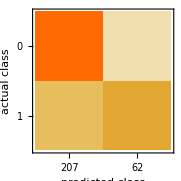
Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 269
Accuracy | (77.32.6) %
Accuracy baseline | (63.92.9) %
Geometric mean of probabilities | 0.591 ± 0.015
Mean cross entropy | 0.527 ± 0.026
Single evaluation time | 5.07 ms/example
Batch evaluation speed | 9.7 examples/ms
-Graphics- |

Classify::mlbddataev: The data being evaluated is not formatted correctly.

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Classify[{g[{3, 22, \"\<male\>\"}, 0], g[{1, 38, \"\<female\>\"}, 1], g[{3, 26, \"\<female\>\"}, 1], g[{1, 35, \"\<female\>\"}, 1], g[{3, 35, \"\<male\>\"}, 0], g[{3, \"\<\>\", \"\<male\>\"}, 0], g[{1, 54, \"\<male\>\"}, 0], g[{3, 2, \"\<male\>\"}, 0], g[{3, 27, \"\<female\>\"}, 1], g[{2, 14, \"\<female\>\"}, 1], «613»}].

```mathematica
ClassifierMeasurements[classif, testSet]
```